STATISTIKA IGRALCEV NOGOMETNEGA KLUBA REAL MADRID

## Tabela UEFA Champions League

```mathematica
SetDirectory["C:\\Users\\Drago\\Desktop\\ROM-master\\projekt_1"]
```

C:\Users\Drago\Desktop\ROM-master\projekt_1

```mathematica
Directory[]
```

C:\Users\Drago\Desktop\ROM-master\projekt_1

```mathematica
Tabela1 = Import["UEFAChampionsLeague.xlsx"]//First;
```

```mathematica
Tabela1 // TableForm
```

Igralci | Višina | Teža | MIN | Goli | Asistence | Rumen | Rdeč | Streli
Carvajal | 173. | 73. | 239. | 0. | 0. | 0. | 0. | 1.
Vallejo | 184. | 79. | 90. | 0. | 0. | 0. | 0. | 0.
Sergio Ramos | 184. | 82. | 329. | 0. | 0. | 2. | 0. | 2.
Varane | 191. | 81. | 270. | 0. | 0. | 1. | 0. | 1.
Nacho | 180. | 76. | 270. | 0. | 0. | 1. | 0. | 1.
Marcelo | 174. | 80. | 344. | 1. | 1. | 0. | 0. | 1.
Odriozola | 176. | 66. | 227. | 0. | 0. | 0. | 0. | 0.
Reguilon | 178. | 68. | 180. | 0. | 0. | 0. | 0. | 1.
Kroos | 183. | 76. | 465. | 1. | 2. | 1. | 0. | 2.
Modric | 172. | 66. | 287. | 0. | 1. | 1. | 0. | 2.
Casemiro | 185. | 84. | 328. | 1. | 0. | 0. | 0. | 1.
Valverde | 181. | 78. | 136. | 0. | 0. | 1. | 0. | 1.
M. Llorente | 184. | 73. | 148. | 0. | 0. | 0. | 0. | 1.
Asensio | 182. | 76. | 230. | 0. | 0. | 0. | 0. | 2.
Isco | 176. | 79. | 251. | 1. | 0. | 1. | 0. | 2.
D. Ceballos | 179. | 70. | 185. | 0. | 0. | 0. | 0. | 1.
Mariano | 182. | 76. | 64. | 1. | 0. | 0. | 0. | 1.
Benzema | 185. | 81. | 425. | 3. | 2. | 0. | 0. | 3.
Bale | 185. | 81. | 367. | 3. | 2. | 0. | 0. | 3.
Lucas Vazquez | 173. | 70. | 328. | 1. | 1. | 0. | 0. | 1.
Vinicius Junior | 177. | 73. | 118. | 0. | 1. | 0. | 0. | 3.

## Glava tabele

```mathematica
GlavaTab[podatki_]:=First[podatki]
```

```mathematica
GlavaTab[Tabela1]
```

{Igralci,Višina,Teža,MIN,Goli,Asistence,Rumen,Rdeč,Streli}

## Podatki v tabeli

```mathematica
Podatki1[podatki_]:=Rest[podatki]
```

```mathematica
Podatki1[Tabela1]
```

{{Carvajal,173.,73.,239.,0.,0.,0.,0.,1.},{Vallejo,184.,79.,90.,0.,0.,0.,0.,0.},{Sergio Ramos,184.,82.,329.,0.,0.,2.,0.,2.},{Varane,191.,81.,270.,0.,0.,1.,0.,1.},{Nacho,180.,76.,270.,0.,0.,1.,0.,1.},{Marcelo,174.,80.,344.,1.,1.,0.,0.,1.},{Odriozola,176.,66.,227.,0.,0.,0.,0.,0.},{Reguilon,178.,68.,180.,0.,0.,0.,0.,1.},{Kroos,183.,76.,465.,1.,2.,1.,0.,2.},{Modric,172.,66.,287.,0.,1.,1.,0.,2.},{Casemiro,185.,84.,328.,1.,0.,0.,0.,1.},{Valverde,181.,78.,136.,0.,0.,1.,0.,1.},{M. Llorente,184.,73.,148.,0.,0.,0.,0.,1.},{Asensio,182.,76.,230.,0.,0.,0.,0.,2.},{Isco,176.,79.,251.,1.,0.,1.,0.,2.},{D. Ceballos,179.,70.,185.,0.,0.,0.,0.,1.},{Mariano,182.,76.,64.,1.,0.,0.,0.,1.},{Benzema,185.,81.,425.,3.,2.,0.,0.,3.},{Bale,185.,81.,367.,3.,2.,0.,0.,3.},{Lucas Vazquez,173.,70.,328.,1.,1.,0.,0.,1.},{Vinicius Junior,177.,73.,118.,0.,1.,0.,0.,3.}}

## Indeks stolpca MIN

```mathematica
IndeksStolpca[podatki_,stolpec_]:=Position[GlavaTab[podatki],stolpec]//First //First
IndeksStolpca[Tabela1,"MIN"]
```

4

## Podatki iz 19-tega stolpca

```mathematica
Vrstica[podatki_,i_]:=Podatki1[podatki][[i]]
Vrstica[Tabela1,19]
```

{Bale,185.,81.,367.,3.,2.,0.,0.,3.}

## Podatki iz stolpca višina

```mathematica
Stolpec[podatki_,stolpec_]:=Transpose[Podatki1[podatki]][[IndeksStolpca[podatki,stolpec]]]
Stolpec[Tabela1,"Višina"]
```

{173.,184.,184.,191.,180.,174.,176.,178.,183.,172.,185.,181.,184.,182.,176.,179.,182.,185.,185.,173.,177.}

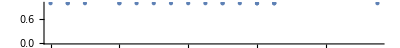

```mathematica
NumberLinePlot[{Stolpec[Tabela1, "Višina"]}]
```

## Povprečje višine

```mathematica
PovprecjeGolov[Tabela1_] := Mean[Stolpec[Tabela1, "Višina"]]
PovprecjeGolov[Tabela1]
```

180.19

## Prikaz teže igralcev z grafom

```mathematica
Stolpec[podatki_,stolpec_]:=Transpose[Podatki1[podatki]][[IndeksStolpca[podatki,stolpec]]]
igralci=Stolpec[Tabela1,"Igralci"];
```

```mathematica
uefa=BarChart3D[{Stolpec[Tabela1, "Teža"]},ChartLabels->igralci,BarSpacing->Large,BarOrigin->Right]
```

-Graphics3D-

## Pozicije igralcev

```mathematica
DodajStolpec[podatki_,imeStolpca_,podatkiStolpec_]:= Append[Transpose[podatki], Prepend[podatkiStolpec, imeStolpca]] // Transpose
```

```mathematica
pozicije = Import["PozicijeIgralcev.xlsx"] //First
```

{{Branilec},{Branilec},{Branilec},{Branilec},{Branilec},{Branilec},{Branilec},{Branilec},{Vezist},{Vezist},{Vezist},{Vezist},{Vezist},{Vezist},{Vezist},{Vezist},{Napadalec},{Napadalec},{Vezist},{Vezist},{Napadalec}}

```mathematica
novaTabela=DodajStolpec[Tabela1,"Pozicije",pozicije]//TableForm
```

Igralci | Višina | Teža | MIN | Goli | Asistence | Rumen | Rdeč | Streli | Pozicije
Carvajal | 173. | 73. | 239. | 0. | 0. | 0. | 0. | 1. | Branilec
Vallejo | 184. | 79. | 90. | 0. | 0. | 0. | 0. | 0. | Branilec
Sergio Ramos | 184. | 82. | 329. | 0. | 0. | 2. | 0. | 2. | Branilec
Varane | 191. | 81. | 270. | 0. | 0. | 1. | 0. | 1. | Branilec
Nacho | 180. | 76. | 270. | 0. | 0. | 1. | 0. | 1. | Branilec
Marcelo | 174. | 80. | 344. | 1. | 1. | 0. | 0. | 1. | Branilec
Odriozola | 176. | 66. | 227. | 0. | 0. | 0. | 0. | 0. | Branilec
Reguilon | 178. | 68. | 180. | 0. | 0. | 0. | 0. | 1. | Branilec
Kroos | 183. | 76. | 465. | 1. | 2. | 1. | 0. | 2. | Vezist
Modric | 172. | 66. | 287. | 0. | 1. | 1. | 0. | 2. | Vezist
Casemiro | 185. | 84. | 328. | 1. | 0. | 0. | 0. | 1. | Vezist
Valverde | 181. | 78. | 136. | 0. | 0. | 1. | 0. | 1. | Vezist
M. Llorente | 184. | 73. | 148. | 0. | 0. | 0. | 0. | 1. | Vezist
Asensio | 182. | 76. | 230. | 0. | 0. | 0. | 0. | 2. | Vezist
Isco | 176. | 79. | 251. | 1. | 0. | 1. | 0. | 2. | Vezist
D. Ceballos | 179. | 70. | 185. | 0. | 0. | 0. | 0. | 1. | Vezist
Mariano | 182. | 76. | 64. | 1. | 0. | 0. | 0. | 1. | Napadalec
Benzema | 185. | 81. | 425. | 3. | 2. | 0. | 0. | 3. | Napadalec
Bale | 185. | 81. | 367. | 3. | 2. | 0. | 0. | 3. | Vezist
Lucas Vazquez | 173. | 70. | 328. | 1. | 1. | 0. | 0. | 1. | Vezist
Vinicius Junior | 177. | 73. | 118. | 0. | 1. | 0. | 0. | 3. | Napadalec

## Tortni diagram golov UEFA Champions League

```mathematica
igralci1=Stolpec[Tabela1,"Igralci"];
```

```mathematica
PieChart3D[{Stolpec[Tabela1, "Goli"]},ChartStyle->"DarkRainbow",ChartLabels->igralci1]
```

-Graphics3D-

## Tabela LaLiga

```mathematica
Tabela2 = Import["LaLiga.xlsx"]//First;
```

```mathematica
Tabela2//TableForm
```

Igralci | Višina | Starost | Teža | MIN | Goli | Asistence | Rumen | Rdeč | Streli
Carvajal | 173. | 27. | 73. | 936. | 1. | 1. | 4. | 0. | 1.
Sergio Ramos | 184. | 32. | 82. | 1620. | 1. | 1. | 2. | 0. | 1.
Varane | 191. | 25. | 81. | 1247. | 1. | 0. | 0. | 0. | 1.
Nacho | 180. | 29. | 76. | 760. | 0. | 0. | 3. | 0. | 0.
Marcelo | 174. | 30. | 80. | 926. | 1. | 0. | 3. | 0. | 1.
Odriozola | 176. | 23. | 66. | 550. | 0. | 1. | 0. | 0. | 0.
Reguilon | 178. | 22. | 68. | 239. | 0. | 0. | 1. | 0. | 0.
Kroos | 183. | 29. | 76. | 1246. | 0. | 1. | 1. | 0. | 1.
Modric | 172. | 33. | 66. | 1291. | 0. | 2. | 3. | 0. | 1.
Casemiro | 185. | 26. | 84. | 991. | 0. | 0. | 2. | 0. | 1.
Valverde | 181. | 20. | 78. | 78. | 0. | 0. | 0. | 0. | 0.
M. Llorente | 184. | 24. | 73. | 281. | 0. | 0. | 0. | 0. | 0.
Asensio | 182. | 23. | 76. | 997. | 1. | 1. | 1. | 0. | 2.
Isco | 176. | 26. | 79. | 594. | 1. | 2. | 1. | 0. | 1.
D. Ceballos | 179. | 22. | 70. | 706. | 1. | 0. | 2. | 0. | 0.
Mariano | 182. | 25. | 76. | 205. | 0. | 0. | 1. | 0. | 2.
Benzema | 185. | 31. | 81. | 1442. | 2. | 2. | 1. | 0. | 3.
Bale | 185. | 29. | 81. | 1098. | 4. | 2. | 3. | 0. | 4.
Lucas Vazquez | 173. | 27. | 70. | 768. | 1. | 2. | 2. | 1. | 1.
Vinicius Junior | 177. | 18. | 73. | 151. | 1. | 0. | 0. | 0. | 1.

## Glava tabele

```mathematica
GlavaTab2[podatki_]:=First[podatki]
GlavaTab2[Tabela2]
```

{Igralci,Višina,Starost,Teža,MIN,Goli,Asistence,Rumen,Rdeč,Streli}

## Podatki v tabeli

```mathematica
Podatki2[podatki_]:=Rest[podatki]
Podatki2[Tabela2]
```

{{Carvajal,173.,27.,73.,936.,1.,1.,4.,0.,1.},{Sergio Ramos,184.,32.,82.,1620.,1.,1.,2.,0.,1.},{Varane,191.,25.,81.,1247.,1.,0.,0.,0.,1.},{Nacho,180.,29.,76.,760.,0.,0.,3.,0.,0.},{Marcelo,174.,30.,80.,926.,1.,0.,3.,0.,1.},{Odriozola,176.,23.,66.,550.,0.,1.,0.,0.,0.},{Reguilon,178.,22.,68.,239.,0.,0.,1.,0.,0.},{Kroos,183.,29.,76.,1246.,0.,1.,1.,0.,1.},{Modric,172.,33.,66.,1291.,0.,2.,3.,0.,1.},{Casemiro,185.,26.,84.,991.,0.,0.,2.,0.,1.},{Valverde,181.,20.,78.,78.,0.,0.,0.,0.,0.},{M. Llorente,184.,24.,73.,281.,0.,0.,0.,0.,0.},{Asensio,182.,23.,76.,997.,1.,1.,1.,0.,2.},{Isco,176.,26.,79.,594.,1.,2.,1.,0.,1.},{D. Ceballos,179.,22.,70.,706.,1.,0.,2.,0.,0.},{Mariano,182.,25.,76.,205.,0.,0.,1.,0.,2.},{Benzema,185.,31.,81.,1442.,2.,2.,1.,0.,3.},{Bale,185.,29.,81.,1098.,4.,2.,3.,0.,4.},{Lucas Vazquez,173.,27.,70.,768.,1.,2.,2.,1.,1.},{Vinicius Junior,177.,18.,73.,151.,1.,0.,0.,0.,1.}}

## Starost igralcev

```mathematica
IndeksStolpca[Tabela2_,stolpec_] := Position[GlavaTab2[Tabela2], stolpec] //First // First
IndeksStolpca[Tabela2, "Starost"]
```

3

```mathematica
VrednostStarosti[Tabela2_,stolpec_] := Transpose[Podatki2[Tabela2]][[IndeksStolpca[Tabela2, stolpec]]]
VrednostStarosti[Tabela2, "Starost"]
```

{27.,32.,25.,29.,30.,23.,22.,29.,33.,26.,20.,24.,23.,26.,22.,25.,31.,29.,27.,18.}

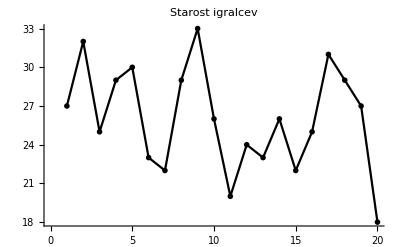

```mathematica
ListLinePlot[{VrednostStarosti[Tabela2, "Starost"]},PlotLabel->"Starost igralcev",PlotTheme->"Monochrome"]
```

## Povprečna starost igralcev

```mathematica
PovprecnaStarost[Tabela2_] := Mean[VrednostStarosti[Tabela2, "Starost"]]
PovprecnaStarost[Tabela2]
```

26.05

## Najstarejši in najmlajši igralec

```mathematica
NajstarejsiIgralec[Tabela2_] := Max[VrednostStarosti[Tabela2, "Starost"]]
NajstarejsiIgralec[Tabela2]
```

33.

```mathematica
NajmlajsiIgralec[Tabela2_] := Min[VrednostStarosti[Tabela2, "Starost"]]
NajmlajsiIgralec[Tabela2]
```

18.

## Prikaz višine igralcev z grafom

```mathematica
igralci2=Stolpec[Tabela2,"Igralci"];
```

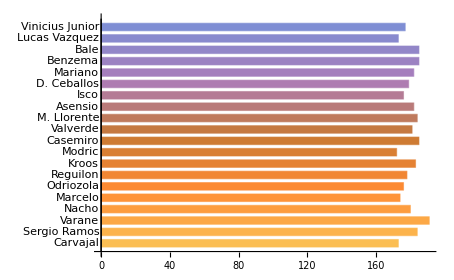

```mathematica
laliga=BarChart[{Stolpec[Tabela2, "Višina"]},ChartLabels->igralci2,BarSpacing->Large, BarOrigin->Left]
```

## Dodajanje novega stolpca

```mathematica
DodajStolpec[podatki_,imeStolpca_,podatkiStolpec_]:= Append[Transpose[podatki], Prepend[podatkiStolpec, imeStolpca]] // Transpose
```

```mathematica
vUre=First[Function[MIN,MIN/60]/@{Stolpec[Tabela2,"MIN"]}//N]
```

{15.6,27.,20.7833,12.6667,15.4333,9.16667,3.98333,20.7667,21.5167,16.5167,1.3,4.68333,16.6167,9.9,11.7667,3.41667,24.0333,18.3,12.8,2.51667}

```mathematica
DodajStolpec[Tabela2,"Ure",vUre]//TableForm
```

Igralci | Višina | Starost | Teža | MIN | Goli | Asistence | Rumen | Rdeč | Streli | Ure
Carvajal | 173. | 27. | 73. | 936. | 1. | 1. | 4. | 0. | 1. | 15.6
Sergio Ramos | 184. | 32. | 82. | 1620. | 1. | 1. | 2. | 0. | 1. | 27.
Varane | 191. | 25. | 81. | 1247. | 1. | 0. | 0. | 0. | 1. | 20.7833
Nacho | 180. | 29. | 76. | 760. | 0. | 0. | 3. | 0. | 0. | 12.6667
Marcelo | 174. | 30. | 80. | 926. | 1. | 0. | 3. | 0. | 1. | 15.4333
Odriozola | 176. | 23. | 66. | 550. | 0. | 1. | 0. | 0. | 0. | 9.16667
Reguilon | 178. | 22. | 68. | 239. | 0. | 0. | 1. | 0. | 0. | 3.98333
Kroos | 183. | 29. | 76. | 1246. | 0. | 1. | 1. | 0. | 1. | 20.7667
Modric | 172. | 33. | 66. | 1291. | 0. | 2. | 3. | 0. | 1. | 21.5167
Casemiro | 185. | 26. | 84. | 991. | 0. | 0. | 2. | 0. | 1. | 16.5167
Valverde | 181. | 20. | 78. | 78. | 0. | 0. | 0. | 0. | 0. | 1.3
M. Llorente | 184. | 24. | 73. | 281. | 0. | 0. | 0. | 0. | 0. | 4.68333
Asensio | 182. | 23. | 76. | 997. | 1. | 1. | 1. | 0. | 2. | 16.6167
Isco | 176. | 26. | 79. | 594. | 1. | 2. | 1. | 0. | 1. | 9.9
D. Ceballos | 179. | 22. | 70. | 706. | 1. | 0. | 2. | 0. | 0. | 11.7667
Mariano | 182. | 25. | 76. | 205. | 0. | 0. | 1. | 0. | 2. | 3.41667
Benzema | 185. | 31. | 81. | 1442. | 2. | 2. | 1. | 0. | 3. | 24.0333
Bale | 185. | 29. | 81. | 1098. | 4. | 2. | 3. | 0. | 4. | 18.3
Lucas Vazquez | 173. | 27. | 70. | 768. | 1. | 2. | 2. | 1. | 1. | 12.8
Vinicius Junior | 177. | 18. | 73. | 151. | 1. | 0. | 0. | 0. | 1. | 2.51667

## Tortni diagram golov LaLige

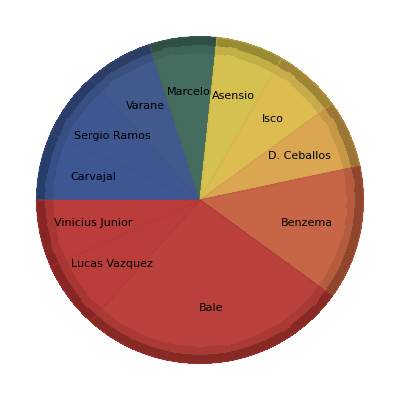

-Graphics-

```mathematica
PieChart[{Stolpec[Tabela2, "Goli"]},ChartStyle->"DarkRainbow",ChartLabels->igralci2,PlotTheme->"Business"]
```